# Levels!

--Jason, August 2024. The purpose of this notebook is to experiment with using the Mathematica constrained quadratic optimizer to attempt to come up with a height function on knots.

We’re going to assign a variable to each of the arcs at a crossing (the overstrand and understrand, so there are going to be 2n variables). The quadratic objective function is just going to be the graph Laplacian of the cycle graph with 2n edges.

The constraint matrix is constructed in the following way: for each {a,b,c,d} in the PD code, we know that a is the incoming lower edge, c is the outgoing lower edge, and b and d are the overstrand. Now we’ll name each of our variables by the outgoing arc, and write down relations in the form {over,under}

```mathematica
BuildConstraintMatrix[PD_] := 
SparseArray[Flatten[MapIndexed[{{#2[[1]],#1[[3]]+1}->-1,{#2[[1]],If[Abs[#1[[2]]-#1[[4]]]==1,Max[#[[{2,4}]]],0]+1}->+1}& ,PD],1],{Length[PD],2Length[PD]}];
```

```mathematica
PD = {{425,137,0,136},{137,1,138,0},{1,135,2,134},{2,144,3,143},{3,127,4,126},{127,5,128,4},{58,5,59,6},{171,7,172,6},{148,8,149,7},{8,72,9,71},{70,10,71,9},{10,164,11,163},{164,12,165,11},{17,13,18,12},{68,13,69,14},{14,168,15,167},{168,16,169,15},{69,17,70,16},{18,166,19,165},{19,185,20,184},{25,21,26,20},{21,25,22,24},{41,23,42,22},{23,43,24,42},{26,183,27,184},{27,162,28,163},{149,28,150,29},{29,178,30,179},{30,174,31,173},{174,32,175,31},{32,176,33,175},{52,34,53,33},{47,34,48,35},{35,152,36,153},{155,36,156,37},{37,156,38,157},{159,38,160,39},{39,46,40,47},{40,182,41,181},{182,44,183,43},{44,161,45,162},{160,45,161,46},{151,49,152,48},{49,151,50,150},{177,51,178,50},{51,177,52,176},{53,181,54,180},{57,55,58,54},{55,129,56,128},{129,57,130,56},{146,60,147,59},{60,74,61,73},{120,61,121,62},{62,117,63,118},{66,63,67,64},{64,120,65,119},{118,66,119,65},{166,68,167,67},{169,72,170,73},{145,74,146,75},{75,144,76,145},{76,122,77,121},{86,78,87,77},{78,89,79,90},{88,79,89,80},{403,80,404,81},{394,82,395,81},{82,399,83,400},{398,83,399,84},{84,394,85,393},{85,404,86,405},{90,88,91,87},{366,91,367,92},{357,93,358,92},{93,357,94,356},{355,95,356,94},{95,355,96,354},{96,375,97,376},{376,97,377,98},{98,377,99,378},{378,99,379,100},{385,101,386,100},{101,387,102,386},{329,102,330,103},{103,330,104,331},{331,104,332,105},{322,105,323,106},{106,327,107,328},{107,320,108,321},{353,109,354,108},{109,351,110,350},{113,111,114,110},{111,352,112,353},{351,112,352,113},{114,339,115,340},{360,116,361,115},{116,360,117,359},{122,424,123,423},{138,124,139,123},{124,134,125,133},{125,143,126,142},{130,416,131,415},{414,132,415,131},{141,133,142,132},{135,425,136,424},{190,140,191,139},{140,190,141,189},{147,170,148,171},{153,158,154,159},{157,154,158,155},{179,173,180,172},{198,185,199,186},{186,195,187,196},{187,412,188,413},{188,420,189,419},{191,407,192,406},{192,421,193,422},{410,193,411,194},{194,409,195,410},{196,418,197,417},{416,198,417,197},{199,339,200,338},{239,200,240,201},{201,234,202,235},{251,203,252,202},{226,204,227,203},{204,272,205,271},{205,285,206,284},{257,207,258,206},{207,259,208,258},{208,281,209,282},{209,262,210,263},{269,210,270,211},{211,270,212,271},{253,212,254,213},{278,213,279,214},{214,255,215,256},{260,215,261,216},{216,259,217,260},{217,257,218,256},{218,289,219,290},{288,219,289,220},{220,287,221,288},{286,221,287,222},{222,285,223,286},{223,272,224,273},{249,224,250,225},{225,250,226,251},{252,227,253,228},{228,278,229,277},{229,290,230,291},{273,231,274,230},{248,231,249,232},{313,232,314,233},{233,314,234,315},{235,334,236,335},{335,236,336,237},{237,336,238,337},{337,238,338,239},{319,240,320,241},{241,318,242,319},{317,242,318,243},{243,300,244,301},{301,244,302,245},{245,302,246,303},{299,246,300,247},{296,248,297,247},{254,280,255,279},{261,280,262,281},{263,269,264,268},{267,265,268,264},{265,283,266,282},{283,267,284,266},{293,275,294,274},{275,295,276,294},{291,276,292,277},{295,293,296,292},{297,306,298,307},{307,298,308,299},{303,310,304,311},{309,304,310,305},{305,308,306,309},{311,316,312,317},{315,312,316,313},{321,329,322,328},{326,324,327,323},{324,333,325,334},{332,325,333,326},{347,341,348,340},{341,349,342,348},{349,343,350,342},{343,364,344,365},{363,344,364,345},{345,362,346,363},{361,346,362,347},{358,365,359,366},{382,367,383,368},{368,383,369,384},{369,389,370,388},{387,371,388,370},{384,371,385,372},{372,379,373,380},{380,373,381,374},{374,381,375,382},{389,396,390,397},{401,390,402,391},{391,400,392,401},{397,392,398,393},{395,402,396,403},{422,405,423,406},{407,420,408,421},{408,412,409,411},{418,413,419,414}};
```

```mathematica
BuildObjectiveFunction[PD_] :=#.#&@KirchhoffMatrix[CycleGraph[2*Length[PD]]]
```

```mathematica
BuildObjectiveFunction[PD]
```

SparseArray[…]

```mathematica
Timing[SuggestedLevels = QuadraticOptimization[BuildObjectiveFunction[PD],{BuildConstraintMatrix[PD],ConstantArray[-2,Length[PD]]}];]
```

{0.059588,Null}

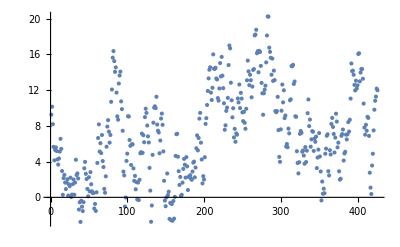

```mathematica
ListPlot[SuggestedLevels]
```

Now we check whether the constraints are actually satisfied:

```mathematica
SuggestedLevels[[PD[[1]]+1]]
```

{11.993,11.2609,9.2609,9.99303}

```mathematica
PD[[1]]+1
```

{426,138,1,137}

Ok, it works here (at least).